```mathematica
β1[ω_,δ_,t_,ϵ_]:=β1[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
Clear[LEFT1]
```

```mathematica
LEFT1[ω_,δ_,t_,ϵ_]:=LEFT1[ω,δ,t,ϵ]=Module[{J=Inverse[β1[ω,0.0001,1,0]],B:=Inverse[β1[ω,0.0001,1,0]],T:=T2[1]},Do[J=PseudoInverse[IdentityMatrix[1]-B.T.J.T].B,10000];J=J]
```

```mathematica
Im[LEFT1[1,0,1,0]][[1,1]]
```

-1.66276

```mathematica
β[ω_,δ_,t_,ϵ_]:=
ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->t]
```

```mathematica
T1[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
(*Import leads *)
```

```mathematica
Lead=Table[ToExpression[Import["Downloads/PhD_new/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

```mathematica
Clear[LEFT,SL,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]](*Module[{unit=Inverse[β[ω,δ,t,ϵ]],J=Inverse[β[ω,δ,t,ϵ]]},Do[J=Inverse[IdentityMatrix[14]-unit.ConjugateTranspose[T1[t]].J.T1[t]].unit,15000];J=J]*)
```

```mathematica
(*Or Generate leads using recursive algorithm*)
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
pris :=pris= ParallelTable[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

```mathematica
pris
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

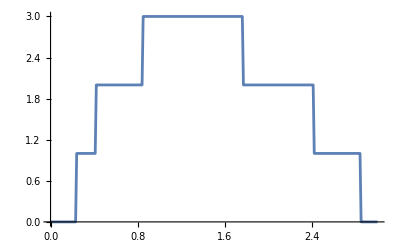

```mathematica
ListLinePlot[pris]
```

```mathematica
(* Conductance using Kubo Formula *)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=s[xstart,xstop,ystart,ystop]=Module[{baseData=f1[ystart,xstart,xstop]},Join@@Table[f1[y,xstart,xstop],{y,ystart+1,ystop}]]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_]:=dist[total]=Table[SortBy[Join[RandomSample[s[1,100,1,14],total]],First],10000]
```

```mathematica
dist[10][[1]]
```

{{17,4},{24,12},{43,4},{47,9},{47,14},{59,11},{63,5},{74,6},{90,3},{97,3}}

```mathematica
unitcelltest2[ω_,total_,number_,unitcell_]:=Module[{J=β[ω,0.0001,1,0]},Do[Module[{currentDist=dist[total][[number]][[loc1]]},If[currentDist[[1]]==unitcell,J=ReplacePart[J,{{currentDist[[2]],currentDist[[2]]}}->ω+I*0.0001-0.5]]],{loc1,total}];
J]
```

```mathematica
inputspectra[ω_,total_,number_]:=Module[{Tin=T1[1],Th=TT[1]},
J1=SL[ω,0.0001,1,0];
sl1= Module[{},Do[J1=Inverse[IdentityMatrix[14]-Inverse[unitcelltest2[ω,total,number,unitcell]].ConjugateTranspose[Tin].J1.Tin].Inverse[unitcelltest2[ω,total,number,unitcell]],{unitcell,100}];J1];Il1=Inverse[IdentityMatrix[14]-sl1.Th.SR[ω,0.0001,1,0].Th].sl1;
Ir1=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].Th.sl1.Th].SR[ω,0.0001,1,0];gdd1= Il1-ConjugateTranspose[Il1];grr1= Ir1-ConjugateTranspose[Ir1];Gnonlocal1= SR[ω,0.0001,1,0].Th.Il1;GNON1= Gnonlocal1-ConjugateTranspose[Gnonlocal1];TRA=Abs[Tr[gdd1.Th.grr1.Th-Th.GNON1.Th.GNON1]];TRA]
```

```mathematica
ParallelTable[{ω,inputspectra[ω,20,1]},{ω,Range[0,3,0.01]}]//AbsoluteTiming
```

```mathematica
Clear[input]
```

```mathematica
input[imp_] :=input[imp] = Monitor[Table[ParallelTable[{ω,inputspectra[ω,imp,n]},{ω,Range[0,3,0.01]}],{n,50}],n]
```

```mathematica
Monitor[Table[input[x],{x,Range[10,90,10]}],x]
```

```mathematica
transmission[x_]:=transmission[x]= ToExpression[Import["~/Downloads/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[x]<>".dat"]]
```

```mathematica
transmission[5]
```

```mathematica
Table[{n,Total[Table[((*input[[1]][[e,2]]/pris[[e,2]]-*)transmission[n][[e,2]]/pris[[e,2]])^2,{e,30,300}]]/270},{n,1,90,2}]
```

```mathematica
Export["~/newmaterial/universal.dat",%32]
```

~/newmaterial/universal.dat

```mathematica
Total[Table[(input[[1]][[e,2]]/pris[[e,2]](*-transmission[n][[e,2]]/pris[[e,2]]*))^2,{e,30,300}]]/270
```

4.71215

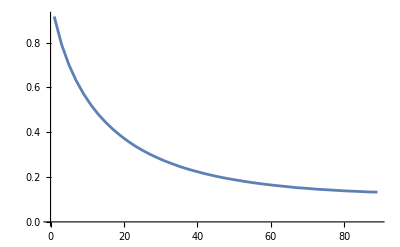

```mathematica
ListPlot[%32,Joined->True]
```

```mathematica
misfit[imp_,x_,y_,n_]:=Module[{m5=input[imp][[n]]},
ρ1=Table[{b,Module[{B1=Transpose[{Range[0,3,0.01],(Abs[Transpose[m5-transmission[b]][[2]]])}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{b,Range[1,110,2]}];lista=ρ1;
ρ1(*,{lista[[Position[lista,Min[lista]][[1,1]]]]}*)]
```

```mathematica
Table[Transpose[misfit[10,1.5,0.0,n]][[2]],{n,50}]
```

```mathematica
Table[Range[1,110,2][[m]],{m,5,55,5}]
```

{9,19,29,39,49,59,69,79,89,99,109}

```mathematica
Table[Module[{},abcd=Table[Transpose[misfit[imp,1.5,0.0,n]][[2]],{n,50}];Around[Table[abcd[[n]][[imp/2]],{n,50}]]],{imp,10,90,10}]
```

{0.001520.00017,0.002080.00015,0.002290.00016,0.002420.00017,0.002490.00017,0.002540.00018,0.002500.00018,0.002460.00014,0.002450.00015}

```mathematica
Table[Abs[Around[Table[Module[{},abc=misfit[imp,1.5,0,n];abc[[Position[abc,Min[abc]][[1,1]]]][[1]]],{n,50}]]],{imp,10,90,10}]
```

{9.61.0,19.81.4,30.11.8,40.43.2,52.5.,63.6.,75.8.,90.9.,99.7.}

```mathematica
Transpose[Join[{%37},{%36}]]
```

{{9.61.0,0.001520.00017},{19.81.4,0.002080.00015},{30.11.8,0.002290.00016},{40.43.2,0.002420.00017},{52.5.,0.002490.00017},{63.6.,0.002540.00018},{75.8.,0.002500.00018},{90.9.,0.002460.00014},{99.7.,0.002450.00015}}

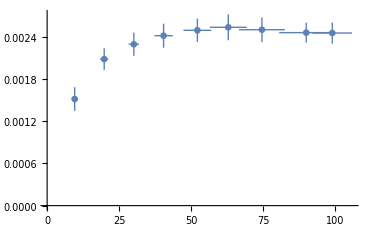

```mathematica
ListPlot[%39]
```

```mathematica
Clear[abc]
abc[n_]:=abc[n]=Flatten[Table[misfit[b,1.5,0.0,n],{b,Range[0.05,0.95,0.1]}],1]
```

```mathematica
abc[1]
```

{{0.05,5,0.000106515},{0.05,10,0.000106151},{0.05,15,0.000105762},{0.05,20,0.000105393},{0.05,25,0.000105042},{0.05,30,0.000104648},{0.05,35,0.0001043},{0.05,40,0.000103931},{0.05,45,0.000103579},{0.05,50,0.000103205},{0.05,55,0.000102926},{0.05,60,0.00010258},{0.05,65,0.000102326},{0.05,70,0.000101983},{0.05,75,0.000101764},{0.05,80,0.000101542},{0.05,85,0.000101334},{0.05,90,0.000101081},{0.15,5,0.000103222},{0.15,10,0.000100573},{0.15,15,0.0000980958},{0.15,20,0.000095577},{0.15,25,0.0000932766},{0.15,30,0.0000910612},{0.15,35,0.0000887311},{0.15,40,0.0000866713},{0.15,45,0.0000845586},{0.15,50,0.0000825531},{0.15,55,0.0000808147},{0.15,60,0.0000788923},{0.15,65,0.0000770227},{0.15,70,0.0000753577},{0.15,75,0.0000736709},{0.15,80,0.0000721295},{0.15,85,0.0000705601},{0.15,90,0.0000689798},{0.25,5,0.0000970195},{0.25,10,0.000089828},{0.25,15,0.0000838371},{0.25,20,0.0000779961},{0.25,25,0.0000726906},{0.25,30,0.0000675491},{0.25,35,0.0000627555},{0.25,40,0.0000589169},{0.25,45,0.0000547496},{0.25,50,0.0000514099},{0.25,55,0.0000480997},{0.25,60,0.0000451042},{0.25,65,0.0000425724},{0.25,70,0.0000399648},{0.25,75,0.0000380444},{0.25,80,0.0000364363},{0.25,85,0.0000346391},{0.25,90,0.0000332251},{0.35,5,0.0000893564},{0.35,10,0.000076494},{0.35,15,0.0000662319},{0.35,20,0.0000571},{0.35,25,0.0000495708},{0.35,30,0.000042957},{0.35,35,0.0000372111},{0.35,40,0.0000333845},{0.35,45,0.0000301576},{0.35,50,0.0000283847},{0.35,55,0.0000273446},{0.35,60,0.0000266173},{0.35,65,0.0000266638},{0.35,70,0.0000268511},{0.35,75,0.0000269301},{0.35,80,0.0000276626},{0.35,85,0.0000283999},{0.35,90,0.0000294313},{0.45,5,0.0000805902},{0.45,10,0.0000625343},{0.45,15,0.0000495371},{0.45,20,0.0000396572},{0.45,25,0.0000327363},{0.45,30,0.0000280201},{0.45,35,0.0000257606},{0.45,40,0.0000251808},{0.45,45,0.000025676},{0.45,50,0.0000268814},{0.45,55,0.0000290696},{0.45,60,0.0000310028},{0.45,65,0.0000332407},{0.45,70,0.0000353218},{0.45,75,0.0000374894},{0.45,80,0.0000397541},{0.45,85,0.0000417374},{0.45,90,0.000043326},{0.55,5,0.0000712968},{0.55,10,0.0000497558},{0.55,15,0.0000358812},{0.55,20,0.0000271587},{0.55,25,0.0000245066},{0.55,30,0.0000250088},{0.55,35,0.0000274142},{0.55,40,0.0000303303},{0.55,45,0.000033739},{0.55,50,0.0000371619},{0.55,55,0.0000398344},{0.55,60,0.0000431667},{0.55,65,0.0000459003},{0.55,70,0.0000480685},{0.55,75,0.0000505282},{0.55,80,0.0000520012},{0.55,85,0.0000540162},{0.55,90,0.0000549412},{0.65,5,0.000062051},{0.65,10,0.0000378713},{0.65,15,0.0000256047},{0.65,20,0.0000232944},{0.65,25,0.0000266398},{0.65,30,0.0000312839},{0.65,35,0.0000360154},{0.65,40,0.0000403874},{0.65,45,0.0000445028},{0.65,50,0.0000482363},{0.65,55,0.0000504273},{0.65,60,0.0000533587},{0.65,65,0.0000553118},{0.65,70,0.0000571458},{0.65,75,0.0000584958},{0.65,80,0.0000598401},{0.65,85,0.0000608753},{0.65,90,0.0000617128},{0.75,5,0.0000535035},{0.75,10,0.0000285553},{0.75,15,0.0000233756},{0.75,20,0.000028046},{0.75,25,0.0000340972},{0.75,30,0.0000399622},{0.75,35,0.0000449442},{0.75,40,0.0000494745},{0.75,45,0.000052558},{0.75,50,0.0000556218},{0.75,55,0.0000575675},{0.75,60,0.0000596485},{0.75,65,0.0000611427},{0.75,70,0.0000623676},{0.75,75,0.0000629175},{0.75,80,0.0000641018},{0.75,85,0.000064485},{0.75,90,0.0000646808},{0.85,5,0.0000459282},{0.85,10,0.0000242684},{0.85,15,0.0000269765},{0.85,20,0.0000345886},{0.85,25,0.000041274},{0.85,30,0.0000472081},{0.85,35,0.0000519023},{0.85,40,0.0000560638},{0.85,45,0.0000582492},{0.85,50,0.0000607002},{0.85,55,0.0000617069},{0.85,60,0.0000632068},{0.85,65,0.0000640041},{0.85,70,0.0000649788},{0.85,75,0.0000653825},{0.85,80,0.0000656159},{0.85,85,0.0000661175},{0.85,90,0.0000661832},{0.95,5,0.0000396541},{0.95,10,0.0000252777},{0.95,15,0.0000321596},{0.95,20,0.0000407967},{0.95,25,0.0000474389},{0.95,30,0.0000528761},{0.95,35,0.0000569726},{0.95,40,0.0000598408},{0.95,45,0.0000616125},{0.95,50,0.0000634393},{0.95,55,0.0000642571},{0.95,60,0.0000653946},{0.95,65,0.0000661023},{0.95,70,0.0000665369},{0.95,75,0.0000658611},{0.95,80,0.0000664376},{0.95,85,0.0000669627},{0.95,90,0.0000664093}}

```mathematica
Table[abc[n][[Position[abc[n],Min[abc[n]]][[1,1]]]],{n,50}]
```

{{0.65,20,0.0000232944},{0.75,15,0.0000243886},{0.55,25,0.0000209139},{0.35,75,0.0000237087},{0.85,10,0.0000231682},{0.75,15,0.0000192817},{0.45,40,0.0000244152},{0.65,20,0.000025086},{0.35,80,0.0000250699},{0.75,15,0.0000230404},{0.75,15,0.0000266853},{0.45,40,0.0000217331},{0.65,15,0.0000229261},{0.75,15,0.0000239179},{0.35,70,0.0000223124},{0.75,15,0.0000262449},{0.55,25,0.0000254388},{0.45,40,0.0000245819},{0.75,15,0.0000242049},{0.85,10,0.0000216296},{0.45,50,0.0000237614},{0.35,65,0.0000267401},{0.35,65,0.0000270962},{0.75,15,0.0000233277},{0.85,10,0.0000242482},{0.75,15,0.0000224699},{0.75,15,0.0000257177},{0.45,40,0.0000213247},{0.95,10,0.0000266455},{0.95,10,0.0000258447},{0.45,40,0.0000240557},{0.55,25,0.0000245147},{0.75,15,0.0000264482},{0.65,20,0.0000214112},{0.45,40,0.0000259973},{0.75,15,0.0000254275},{0.75,15,0.0000239593},{0.55,30,0.0000217433},{0.65,20,0.0000218934},{0.55,25,0.0000242552},{0.65,20,0.000024143},{0.55,25,0.0000221749},{0.45,45,0.0000206247},{0.75,15,0.0000228197},{0.55,25,0.0000245147},{0.85,15,0.0000265106},{0.65,20,0.0000261482},{0.75,15,0.0000230972},{0.75,15,0.0000278637},{0.85,10,0.0000232174}}

```mathematica
Flatten[Table[Table[{x,y,Count[%170,{x,y}]},{x,0.05,1,0.05}],{y,5,70,5}],1]
```

```mathematica
xyz = SortBy[%177,Last]
```

```mathematica
mm=Table[RGBColor[1-xyz[[y,3]]/40,0.02,xyz[[y,3]]/40],{y,1,280,1}]
```

```mathematica
BarLegend[{mm,{0,100}}]
```

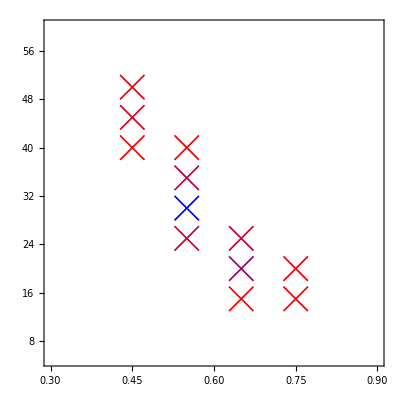

```mathematica
Show[Table[ListPlot[{{xyz[[x,1]],xyz[[x,2]]}},PlotMarkers->{"×",25},PlotStyle->If[xyz[[x,3]]==0,RGBColor[1,1,1],RGBColor[1-xyz[[x,3]]/40,0.02,xyz[[x,3]]/40]],AspectRatio->1,Frame->True,PlotRange->{{0.3,0.9},{5,60}}],{x,280}]]
```

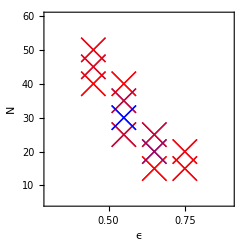

```mathematica
Show[%202,FrameLabel->{{HoldForm[N],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]},AspectRatio->1]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/errornepsi.pdf",%212]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/errornepsi.pdf

```mathematica
SystemOpen["~/Desktop/Thesis/thesis26jun/Images/Chapter3/errornepsi.pdf"]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/scatter_nepsi.dat",%33]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/scatter_nepsi.dat

```mathematica
ListLinePlot[{Table[{0.5,y},{y,Range[0,5.5,0.075]}],Table[{y,30},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}]
```

```mathematica
Plot3D[Interpolation[abc[4]][x,y],{x,0.05,0.95},{y,5.,90.},ColorFunction->"Pastel",PlotRange->All,ImageSize->Full,Boxed->False,Axes->{True,True,False}]
```

```mathematica
Show[ContourPlot[Interpolation[abc[4]][x,y],{x,0.05,0.95},{y,5.,90.},ColorFunction->"BlueGreenYellow",PlotRange->All,ImageSize->Full],ListLinePlot[{Table[{0.5,y},{y,Range[0,90,0.075]}],Table[{y,30},{y,Range[00,1,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}]]
```

```mathematica
Show[%137,FrameLabel->{{HoldForm[N],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/nepsi.pdf",%141]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/nepsi.pdf

```mathematica
SystemOpen["~/Desktop/Thesis/thesis26jun/Images/Chapter3/nepsi.pdf"]
```

```mathematica
Show[%137,FrameLabel->{{HoldForm[N],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

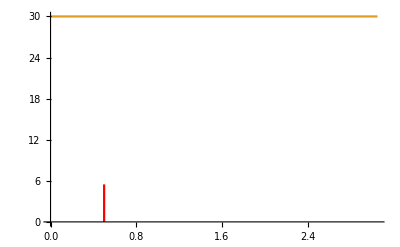

```mathematica
ListLinePlot[{Table[{0.5,y},{y,Range[0,5.5,0.075]}],Table[{y,30},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}]}}]
```

```mathematica
Table[abc[n][[Position[abc[n],Min[abc[n]]][[1,1]]]],{n,50}]
```

{{0.05,5,6.81189×10^7},{0.05,5,6.51975×10^7},{0.05,5,7.7705×10^7},{0.05,5,6.81734×10^7},{0.05,5,6.58666×10^7},{0.05,5,6.06974×10^7},{0.05,5,6.69623×10^7},{0.05,5,6.80406×10^7},{0.05,5,7.85662×10^7},{0.05,5,6.95788×10^7},{0.05,5,6.47985×10^7},{0.05,5,5.78995×10^7},{0.05,5,6.50814×10^7},{0.05,5,6.25496×10^7},{0.05,5,7.04342×10^7},{0.05,5,7.11149×10^7},{0.05,5,7.71098×10^7},{0.05,5,6.90986×10^7},{0.05,5,7.26209×10^7},{0.05,5,6.95603×10^7},{0.05,5,6.00595×10^7},{0.05,5,7.43596×10^7},{0.05,5,7.29686×10^7},{0.05,5,6.72342×10^7},{0.05,5,6.66838×10^7},{0.05,5,6.50666×10^7},{0.05,5,7.29348×10^7},{0.05,5,6.3523×10^7},{0.05,5,6.13167×10^7},{0.05,5,6.86127×10^7},{0.05,5,6.68782×10^7},{0.05,5,6.10822×10^7},{0.05,5,6.87401×10^7},{0.05,5,6.95952×10^7},{0.05,5,6.94372×10^7},{0.05,5,7.13977×10^7},{0.05,5,6.14706×10^7},{0.05,5,6.84023×10^7},{0.05,5,6.60785×10^7},{0.05,5,7.12124×10^7},{0.05,5,6.54302×10^7},{0.05,5,6.07436×10^7},{0.05,5,6.31252×10^7},{0.05,5,7.17192×10^7},{0.05,5,5.47664×10^7},{0.05,5,5.56899×10^7},{0.05,5,6.87149×10^7},{0.05,5,7.33639×10^7},{0.05,5,6.07608×10^7},{0.05,5,6.68757×10^7}}

```mathematica
Interpolation[%62]
```

InterpolatingFunction[…]

```mathematica
ContourPlot[%64[x,y],{x,0.05,0.95},{y,5.,90.}]
```

```mathematica
xyz:=xyz= Table[misfit[0.05,1.5,0.7,n],{n,50}]
```

```mathematica
Table[{y*7,Mean[Table[xyz[[x]][[y]],{x,150}]],StandardDeviation[Table[xyz[[x]][[y]],{x,150}]]},{y,1,8}]
```

{{7,0.0166546,0.00163216},{14,0.00319193,0.000800657},{21,0.00131422,0.000550762},{28,0.00205648,0.000608944},{35,0.00357672,0.000754126},{42,0.00528595,0.000896483},{49,0.00692095,0.0010148},{56,0.00839901,0.00110836}}

```mathematica
Table[{y*10-9,Mean[Table[xyz[[x]][[y]],{x,150}]],StandardDeviation[Table[xyz[[x]][[y]],{x,150}]]},{y,8}]
```

```mathematica
Table[{y*10,Mean[Table[%77[[x]][[y]],{x,150}]],StandardDeviation[Table[%77[[x]][[y]],{x,150}]]},{y,8}]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/errorbar_misfit_7agnr.dat",%129]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/errorbar_misfit_7agnr.dat

```mathematica
misfit[1.5,0,1]//ListPlot
```

```mathematica
ListLinePlot[input[[1]]]
```

```mathematica
Table[misfit[1.5,0.2,n][[2]],{n,10}]
```

```mathematica
ListPlot[%296,Joined->True]
```

```mathematica
Table[Around[Table[Table[Transpose[misfit[0,2,x][[1]]][[2]],{x,10}][[z,m]],{z,10}]],{m,6}]
```

```mathematica
ListLinePlot[%267[[1]][[1]],Frame->True,PlotStyle->Red]
```

```mathematica
Show[ListLinePlot[%267[[1]][[1]],Frame->True,PlotStyle->Red],FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

```mathematica
misfit[3,4.5,10][[1]]
```

```mathematica
Show[ListLinePlot[ParallelTable[{ω,inputspectra[ω,0.0001,1,0,0.5,10,1]},{ω,Range[-3,3,0.01]}]],PlotRange->All]
```

```mathematica
Range[15,75,10]
```

```mathematica
Dimensions[%112]
```

```mathematica
Table[Mean[%111[[x]]],{x,7}]
```

```mathematica
Clear[input]
```

```mathematica
input[ϵ_,total_]:=input[ϵ,total]=Table[(*NIntegrate[Interpolation[*)ParallelTable[{ω,inputspectra[ω,0.0001,1,0,ϵ,total,num]},{ω,Range[0,3,0.01]}](*][x],{x,0,3}]*),{num,10}]
```

```mathematica
Table[Print[x];input[x],{x,10,70,10}]
```

```mathematica
Table[Table[Export["~/PhD/fwi/new_inversion/agnr/input_"<>ToString[conc]<>"_"<>ToString[config]<>"_.dat",input[20][[config]]],{config,100}],{conc,Range[10,70,10]}]
```

```mathematica
ListLinePlot[Import["~/PhD/fwi/new_inversion/agnr/input_20_.dat"]]
```

```mathematica
misfit[ϵ_,conc_,num_,a_,b_]:= Integrate[Interpolation[Table[{input[ϵ,conc][[num]][[x,1]],input[ϵ,conc][[num]][[x,2]]/pris[[x,2]]},{x,301}]][y],{y,a,b}]/Abs[b-a]
```

```mathematica
Table[Print[conc];Mean[Table[Print[nnn];Mean[Table[Mean[Table[misfit[0.3,conc,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]],{conc,10,50,10}]
```

```mathematica
Table[Print[nnn];Mean[Table[Mean[Table[misfit[10,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]
```

```mathematica
Table[Print[nnn];Mean[Table[Mean[Table[misfit[20,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]
```

```mathematica
Table[Print[nnn];Mean[ParallelTable[Mean[Table[misfit[30,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]
```

```mathematica
Table[Print[nnn];Mean[ParallelTable[Mean[Table[misfit[40,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]
```

```mathematica
Table[Print[nnn];Mean[ParallelTable[Mean[Table[misfit[50,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]
```

```mathematica
Table[Print[nnn];Mean[ParallelTable[Mean[Table[misfit[60,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]
```

```mathematica
Table[Print[nnn];Mean[ParallelTable[Mean[Table[misfit[70,nnn,xx,yy],{yy,Range[0.3+xx,3,0.05]}]],{xx,Range[0,2.5,0.05]}]],{nnn,10}]
```

```mathematica
Table[Print[Y];Mean[input[Y]/5.53],{Y,5,60,5}]
```

```mathematica
Configuraional Averaging
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
impurity[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Module[{b=β[ω,δ,t,ϵ]},ReplacePart[b,Table[F[RandomSample[{RandomInteger[{1,14}]},1]]//Flatten,n]->ω+ⅈ*δ-ϵ1]]
```

```mathematica
Clear[dist,list]
```

```mathematica
list[up_,down_]:=Join[Transpose[Join[{Range[1,100]},{RandomSample[Join[Table[0,100-down-up],Table[RandomInteger[{1,14}],up],Table[RandomInteger[{21,40}],down]]]}]]]
```

```mathematica
dist[up_,down_]:=dist[up,down]=Table[list[up,down],5000]
```

```mathematica
CAvg[ω_,δ_,t_,ϵ_,ϵ1_,up_,down_,number_]:= Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{},
(* Distribution of impurities inside the device region *)
b=Module[{},
sl1=Module[{J= SL[ω,0.0001,1,0]},
Do[J=Inverse[IdentityMatrix[14]-Inverse[Module[{κ=β[ω,0.0001,1,0],n= dist[up,down][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].Tin.J.Tin].Inverse[Module[{κ=β[ω,0.0001,1,0],n= dist[up,down][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
CAvg[1,0.0001,1,0,0.5,25,0,1]
```

```mathematica
ListLinePlot[Table[{ω,CAvg[ω,0.0001,1,0,0.5,10,0,2]},{ω,Range[0,3,0.01]}]]
```

```mathematica
Clear[input]
```

```mathematica
input[conc_]:=input[conc]=Table[ParallelTable[{ω,CAvg[ω,0.0001,1,0,0.5,conc,0,num]},{ω,Range[0,3,0.01]}],{num,100}]
```

```mathematica
Table[input[m],{m,10,80,10}]
```

```mathematica
Table[{Mean[Table[NIntegrate[Interpolation[input[z][[y]]][x],{x,0,3}],{y,100}]]/NIntegrate[Interpolation[pris][x],{x,0,3}],StandardDeviation[Table[NIntegrate[Interpolation[input[z][[y]]][x],{x,0,3}],{y,100}]]},{z,10,70,10}]
```

```mathematica
Table[{Mean[Table[NIntegrate[Interpolation[input[z][[y]]][x],{x,0,3}],{y,100}]]/NIntegrate[Interpolation[pris][x],{x,0,3}],StandardDeviation[Table[NIntegrate[Interpolation[input[z][[y]]][x],{x,0,3}],{y,100}]]},{z,10,50,5}]
```

```mathematica
Mean[Table[NIntegrate[Interpolation[%73[[y]]][x],{x,0,3}],{y,1000}]]
```

```mathematica
StandardDeviation[Table[NIntegrate[Interpolation[%73[[y]]][x],{x,0,3}],{y,1000}]]
```

```mathematica
Table[input[x],{x,5,60,5}]
```

```mathematica
ListPlot[%55]
```

```mathematica
(* Size= 100 , M = Number of configurations considered for averaging = 2500 *)
```

```mathematica
avg= Compile[{ω,num},ParallelTable[CAvg[ω,0.0001,1,0,0.5,1,num,100],2500],CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True,CompilationTarget->"C"]
```

```mathematica
(*Generate Configurational average spectras and export! 
num = number of impurities inside the device *)
```

```mathematica
Table[Export["",Table[{ω,avg[ω,num]},{ω,Range[0,3,0.01]}]],{num,Range[5,85,10]}]
```

```mathematica
(*Interpolation (machine learning??)*)
```

```mathematica
(*Import generated averages from above section*)
```

```mathematica
transmission = Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[X]<>".dat"],{X,Range[5,85,10]}]
```

```mathematica
trainingset[ω_]:=Table[5+10*(n-1)->transmission[[n]][[ω*100+1,2]],{n,Range[1,9,1]}]
```

```mathematica
data[num_,ω_]:=Module[{P},P=Predict[trainingset[ω],Method->"NeuralNetwork"]; P[num]]
```

```mathematica
(*This allows us to generate average specta for continuous number of impurities *)
```

```mathematica
Mean[ParallelTable[CAvg[1,0.0001,1,0,0.5,1,50,100],5000]]//AbsoluteTiming
```

```mathematica
data[95,1]//AbsoluteTiming
```

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test95.dat"],PlotStyle->Red,Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}],ListLinePlot[Table[{ω,data[95,ω]},{ω,Range[0,3,0.01]}],PlotStyle->Blue]]
```

```mathematica
Misfit Function
```

```mathematica
transmission100=Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[x]<>".dat"],{x,1,189,2}]
```

```mathematica
Dimensions[transmission100]
```

```mathematica
(* Generate input spectra using kubo formula *)
```

```mathematica
input= ParallelTable[{ω,inputspectra[ω,0.0001,1,0,0.5,56,1]},{ω,Range[0,3,0.01]}]
```

```mathematica
Dimensions[transmission100]
```

```mathematica
Misfit[x_,y_,n_]:=Module[{m5 = input},ρ1:= Table[{(2*ξ-1)/14,Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-transmission100[[ξ]][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{ξ,95}]; 
ρ1]
```

```mathematica
Misfit[2.75,0.,1]
```

```mathematica
Show[ListPlot[Misfit[2.75,0.,1],Joined->True,Frame->True,PlotStyle->Blue,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]},PlotRange->{{0,8},{0,1.2}}],ListLinePlot[Table[{4,y},{y,0,1.2,0.01}],PlotStyle->Red]]
```

```mathematica
ListLinePlot[{Table[{25,y},{y,Range[0.0,20,0.075]}](*,Table[{y,10},{y,Range[0.5,20,0.005]}]*)},PlotStyle->{{Dashing[{0.01,0.01,1*^-2,1*^-2}],Red}(*,{Dashing[{1*^-2,0.01,0.01,1*^-2}],Red}*)},PlotRange->{{0,80},{0,1.2}}]
```

```mathematica
Show[%46,%52]
```

```mathematica
(*Number of impurities obtained from the inversion for given input spectra*)
```

```mathematica
Table[Misfit[2.75,0,n][[Position[Misfit[2.75,0,n],Min[Misfit[2.75,0,n]]][[1,1]]]],{n,100}]
```

```mathematica
ListPlot[Misfit[2.75,0,12],Joined->True,PlotStyle->Red,Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}]
```

```mathematica
Import["~/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/"]
```

```mathematica
Import["~/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/1/*.dat"]//ListLinePlot
```

```mathematica
Import["~/Desktop/Thesis/thesis26jun/Images/Chapter3/misfit_nanb.pdf"]
```

{-Graphics-}